```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 149 Kb

{Utilities`CleanSlate`,TriangleLink`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`,Graphics`Mesh`,Graphics`PolygonUtils`}

```mathematica
Clear[r]
r = 
{ l Sin[θ[t]] , 0 , -l Cos[θ[t]]  }
```

{l Sin[θ[t]],0,-l Cos[θ[t]]}

```mathematica
Clear[Ω]
Ω = 
{ 0 , 0 , ω }
```

{0,0,ω}

```mathematica
D[r, t]
```

{l Cos[θ[t]] θ'[t],0,l Sin[θ[t]] θ'[t]}

```mathematica
Cross[ Ω , r ]
```

{0,l ω Sin[θ[t]],0}

```mathematica
D[r, t] + Cross[ Ω , r ]
```

{l Cos[θ[t]] θ'[t],l ω Sin[θ[t]],l Sin[θ[t]] θ'[t]}

```mathematica
( D[r, t] + Cross[ Ω , r ] ) . ( D[r, t] + Cross[ Ω , r ] )
```

l^2 ω^2 Sin[θ[t]]^2+l^2 Cos[θ[t]]^2 θ'[t]^2+l^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
( D[r, t] + Cross[ Ω , r ] ) . ( D[r, t] + Cross[ Ω , r ] )  // Simplify
```

l^2 (ω^2 Sin[θ[t]]^2+θ'[t]^2)

```mathematica
Clear[T]
T = 
1/2 m ( D[r, t] + Cross[ Ω , r ] ) . ( D[r, t] + Cross[ Ω , r ] )  // Simplify  ;
T // pdConv
```

1/2 l^2 m (ω^2 sin^2(θ(t))+((∂θ(t))/(∂t))^2)

```mathematica
r
r[[3]]
```

{l Sin[θ[t]],0,-l Cos[θ[t]]}

-l Cos[θ[t]]

```mathematica
Clear[V]
V = m g ( r[[3]] )
```

-g l m Cos[θ[t]]

```mathematica
Clear[ℒ]
ℒ = T - V  ;
ℒ // pdConv
```

g l m cos(θ(t))+1/2 l^2 m (ω^2 sin^2(θ(t))+((∂θ(t))/(∂t))^2)

```mathematica
Clear[q]
q = θ[t]
```

θ[t]

```mathematica
D[ D[ ℒ , D[q, t] ], t ]  - D[ ℒ , q ]
```

g l m Sin[θ[t]]-l^2 m ω^2 Cos[θ[t]] Sin[θ[t]]+l^2 m θ''[t]

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // pdConv
```

l m (sin(θ(t)) (l ω^2 cos(θ(t))-g)-l (∂^2 θ(t))/(∂t^2))==0

```mathematica
Clear[parameters]
parameters = { 
m-> 20 , 
g-> 9.8 , 
ω -> 0.5 ,
l-> 0.3 
} ;
parameters // TableForm
```

m→20
g→9.8
ω→0.5
l→0.3

```mathematica
eqs /. parameters  // Expand
```

-58.8 Sin[θ[t]]+0.45 Cos[θ[t]] Sin[θ[t]]-1.8 θ''[t]==0

```mathematica
Clear[ics]
ics = { 
θ[0] == π/12 , 
θ'[0] == 0 
} ;
ics // TableForm
```

θ[0]==π/12
θ'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ { eqs }  /. parameters , ics ] , q , { t, 0, 100 } ] ]
```

{θ[t]→InterpolatingFunction[…][t]}

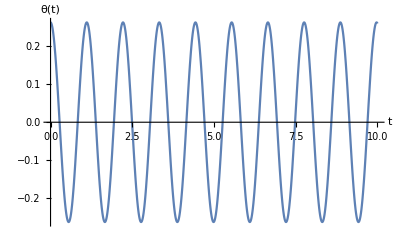

```mathematica
Plot[ q /. solution[t] , { t, 0, 10 } , AxesLabel-> { t , q }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 1 ,75 , 0.5  } ]
```

```mathematica
eqs
eqs[[1,3]]
eqs[[1,3]] /. θ''[t] -> 0
```

l m ((-g+l ω^2 Cos[θ[t]]) Sin[θ[t]]-l θ''[t])==0

(-g+l ω^2 Cos[θ[t]]) Sin[θ[t]]-l θ''[t]

(-g+l ω^2 Cos[θ[t]]) Sin[θ[t]]

```mathematica
Solve[ eqs /. θ''[t]-> 0 , θ[t] ]   /. C[1]-> 0
```

{{θ[t]→0},{θ[t]→π},{θ[t]→ArcTan[g/(l ω^2),-(√(-g^2+l^2 ω^4))/(l ω^2)]},{θ[t]→ArcTan[g/(l ω^2),(√(-g^2+l^2 ω^4))/(l ω^2)]}}

```mathematica
(* REDO This *)
```